```mathematica
Monitor[With[{all=allGraphs6},
With[{sixKeysPlanar=Select[Keys[all],VertexCount[all[#,"graph"]]==6&&PlanarGraphQ[all[#,"graph"]]&]},
TableForm[GatherBy[Table[{
Length[Select[sixKeysPlanar,MemberQ[ListofVars[all[#,"colofour"]],all[k,"colofour"]]&]]/Length[sixKeysPlanar],
Length[Select[sixKeysPlanar,!MemberQ[ListofVars[all[#,"colofour"]],all[k,"colofour"]]&]]/Length[sixKeysPlanar],
With[{p=Labeled[all[k,"graph"],k] },
If[MemberQ[alfa1s,k],Framed[p],p]]
 },{k,allGraphs6AtomKeys//Sort}]//Sort,First], TableDepth->2]
]
],k]
```

{1/32071,32070/32071,-Graphics-14348906} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{32/32071,32039/32071,-Graphics-14169481} | {32/32071,32039/32071,-Graphics-14289097} | {32/32071,32039/32071,-Graphics-13810649} | {32/32071,32039/32071,-Graphics-12734549} | {32/32071,32039/32071,-Graphics-9536777} | {32/32071,32039/32071,-Graphics-7203977} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{256/32071,31815/32071,-Graphics-14109674} | {256/32071,31815/32071,-Graphics-13631242} | {256/32071,31815/32071,-Graphics-13750846} | {256/32071,31815/32071,-Graphics-12196778} | {256/32071,31815/32071,-Graphics-11957786} | {256/32071,31815/32071,-Graphics-12555286} | {256/32071,31815/32071,-Graphics-12674794} | {256/32071,31815/32071,-Graphics-7961786} | {256/32071,31815/32071,-Graphics-7262266} | {256/32071,31815/32071,-Graphics-7378846} | {256/32071,31815/32071,-Graphics-7728602} | {256/32071,31815/32071,-Graphics-9011642} | {256/32071,31815/32071,-Graphics-8778266} | {256/32071,31815/32071,-Graphics-9361726} | {256/32071,31815/32071,-Graphics-9478426} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{511/32071,31560/32071,-Graphics-13571441} | {511/32071,31560/32071,-Graphics-12017533} | {511/32071,31560/32071,-Graphics-12137029} | {511/32071,31560/32071,-Graphics-12495533} | {511/32071,31560/32071,-Graphics-7437137} | {511/32071,31560/32071,-Graphics-7786897} | {511/32071,31560/32071,-Graphics-7903489} | {511/32071,31560/32071,-Graphics-8836609} | {511/32071,31560/32071,-Graphics-8953297} | {511/32071,31560/32071,-Graphics-9303377} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{512/32071,31559/32071,-Graphics-14109673} | {512/32071,31559/32071,-Graphics-13631233} | {512/32071,31559/32071,-Graphics-13750843} | {512/32071,31559/32071,-Graphics-12555205} | {512/32071,31559/32071,-Graphics-12674767} | {512/32071,31559/32071,-Graphics-12196535} | {512/32071,31559/32071,-Graphics-9359539} | {512/32071,31559/32071,-Graphics-7201699} | {512/32071,31559/32071,-Graphics-9477697} | {512/32071,31559/32071,-Graphics-7203217} | {512/32071,31559/32071,-Graphics-9005081} | {512/32071,31559/32071,-Graphics-7197161} | {512/32071,31559/32071,-Graphics-7942103} | {512/32071,31559/32071,-Graphics-7183943} | {512/32071,31559/32071,-Graphics-7174817} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{2044/32071,30027/32071,-Graphics-13571431} | {2044/32071,30027/32071,-Graphics-13571429} | {2044/32071,30027/32071,-Graphics-13571437} | {2044/32071,30027/32071,-Graphics-12017443} | {2044/32071,30027/32071,-Graphics-11957695} | {2044/32071,30027/32071,-Graphics-12495451} | {2044/32071,30027/32071,-Graphics-12495425} | {2044/32071,30027/32071,-Graphics-12136999} | {2044/32071,30027/32071,-Graphics-11957755} | {2044/32071,30027/32071,-Graphics-12495505} | {2044/32071,30027/32071,-Graphics-12017281} | {2044/32071,30027/32071,-Graphics-11957531} | {2044/32071,30027/32071,-Graphics-12136783} | {2044/32071,30027/32071,-Graphics-12017209} | {2044/32071,30027/32071,-Graphics-11957435} | {2044/32071,30027/32071,-Graphics-12136759} | {2044/32071,30027/32071,-Graphics-7784629} | {2044/32071,30027/32071,-Graphics-7259989} | {2044/32071,30027/32071,-Graphics-7726333} | {2044/32071,30027/32071,-Graphics-8834413} | {2044/32071,30027/32071,-Graphics-8776069} | {2044/32071,30027/32071,-Graphics-9301189} | {2044/32071,30027/32071,-Graphics-9300461} | {2044/32071,30027/32071,-Graphics-7200941} | {2044/32071,30027/32071,-Graphics-7902733} | {2044/32071,30027/32071,-Graphics-7378087} | {2044/32071,30027/32071,-Graphics-7727845} | {2044/32071,30027/32071,-Graphics-8952565} | {2044/32071,30027/32071,-Graphics-8777533} | {2044/32071,30027/32071,-Graphics-9302647} | {2044/32071,30027/32071,-Graphics-7430333} | {2044/32071,30027/32071,-Graphics-7255453} | {2044/32071,30027/32071,-Graphics-7372039} | {2044/32071,30027/32071,-Graphics-8830039} | {2044/32071,30027/32071,-Graphics-8771693} | {2044/32071,30027/32071,-Graphics-8946733} | {2044/32071,30027/32071,-Graphics-8827861} | {2044/32071,30027/32071,-Graphics-7194901} | {2044/32071,30027/32071,-Graphics-8768789} | {2044/32071,30027/32071,-Graphics-7194149} | {2044/32071,30027/32071,-Graphics-8946007} | {2044/32071,30027/32071,-Graphics-7196407} | {2044/32071,30027/32071,-Graphics-7417211} | {2044/32071,30027/32071,-Graphics-7242259} | {2044/32071,30027/32071,-Graphics-7358893} | {2044/32071,30027/32071,-Graphics-7767133} | {2044/32071,30027/32071,-Graphics-7708811} | {2044/32071,30027/32071,-Graphics-7883779} | {2044/32071,30027/32071,-Graphics-7410893} | {2044/32071,30027/32071,-Graphics-7177613} | {2044/32071,30027/32071,-Graphics-7233835} | {2044/32071,30027/32071,-Graphics-7175515} | {2044/32071,30027/32071,-Graphics-7351873} | {2044/32071,30027/32071,-Graphics-7176913} | {2044/32071,30027/32071,-Graphics-7765027} | {2044/32071,30027/32071,-Graphics-7181827} | {2044/32071,30027/32071,-Graphics-7706003} | {2044/32071,30027/32071,-Graphics-7181123} | {2044/32071,30027/32071,-Graphics-7883077} | {2044/32071,30027/32071,-Graphics-7183237}
{4088/32071,27983/32071,-Graphics-13571428} | {4088/32071,27983/32071,-Graphics-12495424} | {4088/32071,27983/32071,-Graphics-12017200} | {4088/32071,27983/32071,-Graphics-12136756} | {4088/32071,27983/32071,-Graphics-9300460} | {4088/32071,27983/32071,-Graphics-7200940} | {4088/32071,27983/32071,-Graphics-8827852} | {4088/32071,27983/32071,-Graphics-7194892} | {4088/32071,27983/32071,-Graphics-8946004} | {4088/32071,27983/32071,-Graphics-7196404} | {4088/32071,27983/32071,-Graphics-7764946} | {4088/32071,27983/32071,-Graphics-7181746} | {4088/32071,27983/32071,-Graphics-7174726} | {4088/32071,27983/32071,-Graphics-7883050} | {4088/32071,27983/32071,-Graphics-7183210} | {4088/32071,27983/32071,-Graphics-7174786} | {4088/32071,27983/32071,-Graphics-7410650} | {4088/32071,27983/32071,-Graphics-7177370} | {4088/32071,27983/32071,-Graphics-7174466} | {4088/32071,27983/32071,-Graphics-7174562} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{4096/32071,27975/32071,-Graphics-11957666} | {4096/32071,27975/32071,-Graphics-11957458} | {4096/32071,27975/32071,-Graphics-11957506} | {4096/32071,27975/32071,-Graphics-7725578} | {4096/32071,27975/32071,-Graphics-8775338} | {4096/32071,27975/32071,-Graphics-7253194} | {4096/32071,27975/32071,-Graphics-8769514} | {4096/32071,27975/32071,-Graphics-7371286} | {4096/32071,27975/32071,-Graphics-8770966} | {4096/32071,27975/32071,-Graphics-7235932} | {4096/32071,27975/32071,-Graphics-7352572} | {4096/32071,27975/32071,-Graphics-7240144} | {4096/32071,27975/32071,-Graphics-7706704} | {4096/32071,27975/32071,-Graphics-7358188} | {4096/32071,27975/32071,-Graphics-7708108} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{8157/32071,23914/32071,-Graphics-11957665} | {8157/32071,23914/32071,-Graphics-11957449} | {8157/32071,23914/32071,-Graphics-11957423} | {8157/32071,23914/32071,-Graphics-11957425} | {8157/32071,23914/32071,-Graphics-11957503} | {8157/32071,23914/32071,-Graphics-11957431} | {8157/32071,23914/32071,-Graphics-7725577} | {8157/32071,23914/32071,-Graphics-8775337} | {8157/32071,23914/32071,-Graphics-7253185} | {8157/32071,23914/32071,-Graphics-8769505} | {8157/32071,23914/32071,-Graphics-8768777} | {8157/32071,23914/32071,-Graphics-7194137} | {8157/32071,23914/32071,-Graphics-8768779} | {8157/32071,23914/32071,-Graphics-7194139} | {8157/32071,23914/32071,-Graphics-7371283} | {8157/32071,23914/32071,-Graphics-8770963} | {8157/32071,23914/32071,-Graphics-8768785} | {8157/32071,23914/32071,-Graphics-7194145} | {8157/32071,23914/32071,-Graphics-7240063} | {8157/32071,23914/32071,-Graphics-7706623} | {8157/32071,23914/32071,-Graphics-7705895} | {8157/32071,23914/32071,-Graphics-7181015} | {8157/32071,23914/32071,-Graphics-7233745} | {8157/32071,23914/32071,-Graphics-7175425} | {8157/32071,23914/32071,-Graphics-7174697} | {8157/32071,23914/32071,-Graphics-7705921} | {8157/32071,23914/32071,-Graphics-7181041} | {8157/32071,23914/32071,-Graphics-7358161} | {8157/32071,23914/32071,-Graphics-7708081} | {8157/32071,23914/32071,-Graphics-7351843} | {8157/32071,23914/32071,-Graphics-7176883} | {8157/32071,23914/32071,-Graphics-7705975} | {8157/32071,23914/32071,-Graphics-7181095} | {8157/32071,23914/32071,-Graphics-7235689} | {8157/32071,23914/32071,-Graphics-7352329} | {8157/32071,23914/32071,-Graphics-7233511} | {8157/32071,23914/32071,-Graphics-7175191} | {8157/32071,23914/32071,-Graphics-7351603} | {8157/32071,23914/32071,-Graphics-7176643} | {8157/32071,23914/32071,-Graphics-7233583} | {8157/32071,23914/32071,-Graphics-7175263} | {8157/32071,23914/32071,-Graphics-7174537} | {8157/32071,23914/32071,-Graphics-7351627} | {8157/32071,23914/32071,-Graphics-7176667} | {8157/32071,23914/32071,-Graphics-7174489} |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{16227/32071,15844/32071,-Graphics-11957422} | {16227/32071,15844/32071,-Graphics-8768776} | {16227/32071,15844/32071,-Graphics-7194136} | {16227/32071,15844/32071,-Graphics-7705894} | {16227/32071,15844/32071,-Graphics-7181014} | {16227/32071,15844/32071,-Graphics-7174696} | {16227/32071,15844/32071,-Graphics-7233502} | {16227/32071,15844/32071,-Graphics-7175182} | {16227/32071,15844/32071,-Graphics-7174456} | {16227/32071,15844/32071,-Graphics-7174454} | {16227/32071,15844/32071,-Graphics-7174480} | {16227/32071,15844/32071,-Graphics-7351600} | {16227/32071,15844/32071,-Graphics-7176640} | {16227/32071,15844/32071,-Graphics-7174462} | {16227/32071,15844/32071,-Graphics-7174534} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  | 
{1,0,-Graphics-7174453} |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |  |

```mathematica
2^15-32071
```

697

```mathematica
FactorInteger[697]
```

{{17,1},{41,1}}

```mathematica
With[{g=ReadGrof[100]},
{VertexCount[g],EdgeCount[g]}]
```

{10,24}

```mathematica
TriangleNumber[6]
```

21

```mathematica
3N-6/.N->10
```

24

```mathematica
n(n-1)/2-(3n-6)/.n->10
```

21

```mathematica
EdgeCount[CompleteGraph[10]]
```

45

```mathematica
Map[Map[If[SymbolLevel[#]<5,Framed[#],#]&,FindFullFormula1234[#]]&,{ReadGrof[10000]}]
```

{{v179ax268x34cx5bd,v1479x268x3acx5bd,v179dx268x3acx45b,v1789x246x3acx5bd}}

```mathematica
SymbolToColoring[v1479x268x3acx5bd]
```

{1→RGBColor[1, 0, 0],4→RGBColor[1, 0, 0],7→RGBColor[1, 0, 0],9→RGBColor[1, 0, 0],2→RGBColor[0, 0, 1],6→RGBColor[0, 0, 1],8→RGBColor[0, 0, 1],3→RGBColor[1, 1, 0],10→RGBColor[1, 1, 0],12→RGBColor[1, 1, 0],5→RGBColor[0, 1, 0],11→RGBColor[0, 1, 0],13→RGBColor[0, 1, 0]}

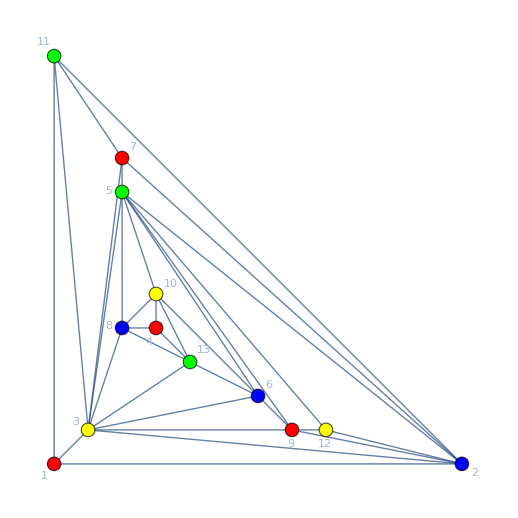

```mathematica
Graph[ReadGrof[10000],VertexLabels->"Name", GraphLayout->"PlanarEmbedding", VertexStyle->SymbolToColoring[v1479x268x3acx5bd], VertexSize->Large]
```

```mathematica
Table[VertexCount[Graph[plantri[[k]]]],{k,50}]
```

{12,14,15,16,16,16,17,17,17,17,18,18,18,18,18,18,18,18,18,18,18,18,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,20,20,20,20,20}

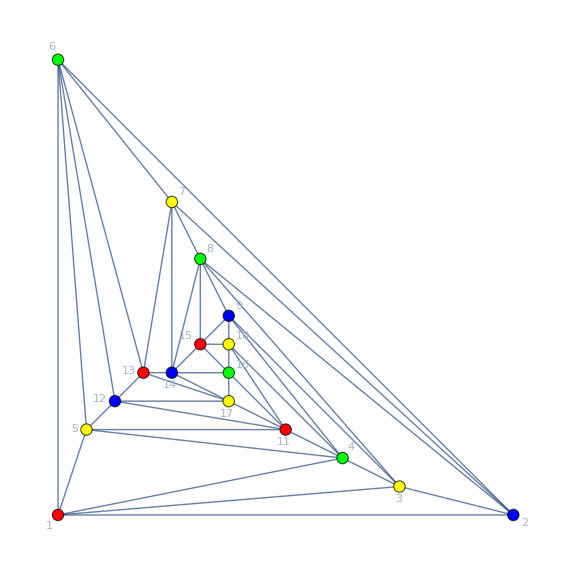

```mathematica
With[{g=Graph[plantri[[7]]]},
Graph[g,VertexLabels->"Name", GraphLayout->"PlanarEmbedding", VertexStyle->SymbolToColoring[First[FindFullFormula1234[g]]], VertexSize->Large]]
```